## ^163Lu - March 2020 Energies

### Fitting the experimental energies

```mathematica
TSD1={{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
TSD2={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
TSD3={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
TSD4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
```

```mathematica
spins=Join[Table[TSD1[[i,1]],{i,1,Length[TSD1]}],Table[TSD2[[i,1]],{i,1,Length[TSD2]}],Table[TSD3[[i,1]],{i,1,Length[TSD3]}],Table[TSD4[[i,1]],{i,1,Length[TSD4]}]];
ExperimentalEnergies=Join[Table[TSD1[[i,2]],{i,1,Length[TSD1]}],Table[TSD2[[i,2]],{i,1,Length[TSD2]}],Table[TSD3[[i,2]],{i,1,Length[TSD3]}],Table[TSD4[[i,2]],{i,1,Length[TSD4]}]];
```

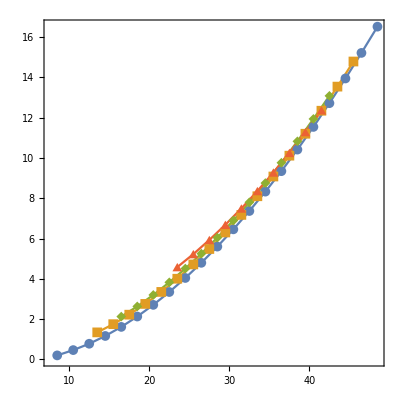

```mathematica
ListPlot[{TSD1,TSD2,TSD3,TSD4},Frame->True,Axes->False,Joined->True,AspectRatio->1,PlotMarkers->{Automatic, Medium}]
```

## Formulas

```mathematica
moi[k_,i0_,γ_,β_]:=i0/(1+(5/(16π))^(1/2)*β)*(1-(5/(4π))^(1/2)β*Cos[γ*π/180+2/3 π*k]);
a1[i0_,γ_,β_]:=1/(2*moi[1,i0,γ,β]);
a2[i0_,γ_,β_]:=1/(2*moi[2,i0,γ,β]);
a3[i0_,γ_,β_]:=1/(2*moi[3,i0,γ,β]);
```

```mathematica
hMin[spin_,oddSpin_,i0_,v_,γ_,β_]:=(a2[i0,γ,β]+a3[i0,γ,β])*(spin+oddSpin)/2+a1[i0,γ,β]*(spin-oddSpin)^2-v*(2oddSpin-1)/(oddSpin+1)*Sin[γ*π/180+π/6];
b1[spin_,oddSpin_,i0_,v_,γ_,β_]:=-1*(((2spin-1)(a3[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])((2spin-1)(a2[i0,γ,β]-a1[i0,γ,β])+2*oddSpin*a1[i0,γ,β])+8spin*oddSpin*a2[i0,γ,β]*a3[i0,γ,β]+((2oddSpin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2oddSpin-1)*(a2[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))2 √3 Sin[γ*π/180]));
c1[spin_,oddSpin_,i0_,v_,γ_,β_]:=(((2spin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])*((2oddSpin-1)*(a3[i0,γ,β]-a1[i0,γ,β])+2spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin(oddSpin+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4spin*oddSpin*a3[i0,γ,β]^2)*(((2spin-1)*(a2[i0,γ,β]-a1[i0,γ,β])+2oddSpin*a1[i0,γ,β])*((2oddSpin-1)(a2[i0,γ,β]-a1[i0,γ,β])+2*spin*a1[i0,γ,β]+v*(2oddSpin-1)/(oddSpin*(oddSpin+1))2 √3 Sin[γ*π/180])-4spin*oddSpin*a2[i0,γ,β]^2);
Omega1[spin_,oddSpin_,i0_,v_,γ_,β_]:=√(1/2(-b1[spin,oddSpin,i0,v,γ,β]+(b1[spin,oddSpin,i0,v,γ,β]^2-4c1[spin,oddSpin,i0,v,γ,β])^(1/2)));
Omega2[spin_,oddSpin_,i0_,v_,γ_,β_]:=√(1/2(-b1[spin,oddSpin,i0,v,γ,β]-(b1[spin,oddSpin,i0,v,γ,β]^2-4c1[spin,oddSpin,i0,v,γ,β])^(1/2)));
```

```mathematica
energyExpression[n1_,n2_,spin_,oddSpin_,i0_,v_,γ_,β_]:=hMin[spin,oddSpin,i0,v,γ,β]+Omega1[spin,oddSpin,i0,v,γ,β]*(n1+1/2)+Omega2[spin,oddSpin,i0,v,γ,β]*(n2+1/2);
e0[i0_,v_,γ_,β_]:=energyExpression[0,0,6.5,6.5,i0,v,γ,β];
energyTSD1[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[0,0,spin,6.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[0,0,spin,6.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
energyTSD2[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[1,0,spin-1,6.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[1,0,spin-1,6.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
energyTSD3[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[2,0,spin-2,6.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[2,0,spin-2,6.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
energyTSD4[spin_,i0_,v_,γ_,β_]:=If[Im[energyExpression[3,0,spin-3,4.5,i0,v,γ,β]-e0[i0,v,γ,β]]==0,energyExpression[3,0,spin-3,4.5,i0,v,γ,β]-e0[i0,v,γ,β],10^11];
```

## RMS fit

```mathematica
RMS[expdata_,thdata_]:=√(Sum[(expdata[[i]]-thdata[[i]])^2,{i,1,Length[expdata]}]/(Length[expdata]-1));
```

## generate theoretical energies from free parameter set X

```mathematica
cppParams={51.56,0.0307,17,0.38};
tsd1Th=Table[energyTSD1[TSD1[[i,1]],cppParams[[1]],cppParams[[2]],cppParams[[3]],cppParams[[4]]],{i,1,Length[TSD1]}];
tsd2Th=Table[energyTSD2[TSD2[[i,1]],cppParams[[1]],cppParams[[2]],cppParams[[3]],cppParams[[4]]],{i,1,Length[TSD2]}];
tsd3Th=Table[energyTSD3[TSD3[[i,1]],cppParams[[1]],cppParams[[2]],cppParams[[3]],cppParams[[4]]],{i,1,Length[TSD3]}];
tsd4Th=Table[energyTSD4[TSD4[[i,1]],cppParams[[1]],cppParams[[2]],cppParams[[3]],cppParams[[4]]],{i,1,Length[TSD4]}];
TheoreticalEnergies=Join[tsd1Th,tsd2Th,tsd3Th,tsd4Th];
TSD1Th=Table[{TSD1[[i,1]],tsd1Th[[i]]},{i,1,Length[TSD1]}];
TSD2Th=Table[{TSD2[[i,1]],tsd2Th[[i]]},{i,1,Length[TSD2]}];
TSD3Th=Table[{TSD3[[i,1]],tsd3Th[[i]]},{i,1,Length[TSD3]}];
TSD4Th=Table[{TSD4[[i,1]],tsd4Th[[i]]},{i,1,Length[TSD4]}];
dataX=Join[Insert[#,1,1]&/@TSD1,Insert[#,2,1]&/@TSD2,Insert[#,3,1]&/@TSD3,Insert[#,4,1]&/@TSD4];
```

```mathematica
RMS[ExperimentalEnergies,TheoreticalEnergies]
```

0.541921

```mathematica
TSD4Th
```

{{23.5,4.35287},{25.5,5.14738},{27.5,6.01498},{29.5,6.9558},{31.5,7.96994},{33.5,9.05748},{35.5,10.2185},{37.5,11.4531},{39.5,12.7612},{41.5,14.1429}}

## Fit - all values

```mathematica
(*nlm=NonlinearModelFit[dataX,{Boole[id==1]*energyTSD1[x,a,b,cppParams[[3]],cppParams[[4]]]+Boole[id==2]*energyTSD2[x,a,b,cppParams[[3]],cppParams[[4]]]+Boole[id==3]*energyTSD3[x,a,b,cppParams[[3]],cppParams[[4]]]+Boole[id==4]*energyTSD4[x,a,b,cppParams[[3]],cppParams[[4]]],energyTSD4[TSD4[[6,1]],a,b,cppParams[[3]],cppParams[[4]]]==TSD4[[6,2]],b>0.1,b<1.0},{a,b},{id,x}];
group3=nlm["BestFitParameters"];
group3*)
```

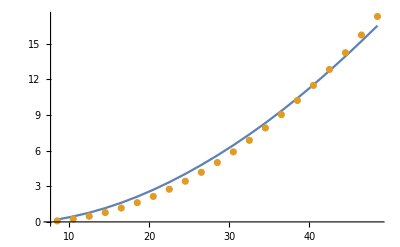

```mathematica
ListPlot[{TSD1,TSD1Th},Joined->{True,False}]
```

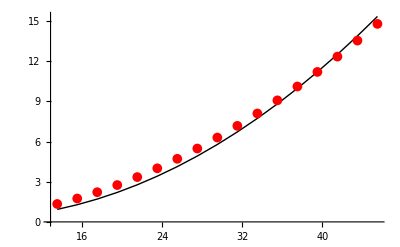

```mathematica
ListPlot[{TSD2,TSD2Th},Joined->{False,True},PlotStyle->{{Red},{Black,Thick}},PlotMarkers->{{Automatic, Medium},None}]
```

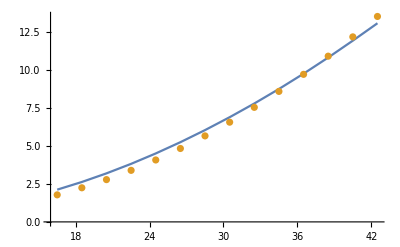

```mathematica
ListPlot[{TSD3,TSD3Th},Joined->{True,False}]
```

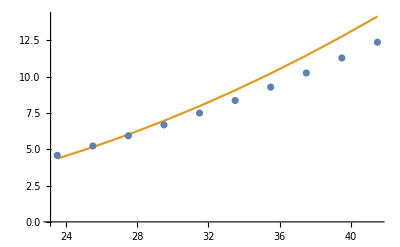

```mathematica
ListPlot[{TSD4,TSD4Th},Joined->{False,True}]
```